```mathematica
ClearAll["Global'*"]
ex={1,0,0};ey={0,1,0};ez={0,0,1};
Vinf=β*y*ex;
Einf = 1/2(Grad[Vinf,{x,y,z}]+Transpose@Grad[Vinf,{x,y,z}])

Eij={{E11,E12,E13},{E21,E22,E23},{E31,E32,E33}};
r=√(x^2+y^2+z^2);
X={x,y,z};
(*Straining Velocity Field and Pressure*)
u=-(5 a^3)/2 X((X.(Einf.X))/r^5)-a^5/2((Einf.X+X.Einf)/r^5-(5X (X.(Einf.X)))/r^7)
```

{{0,β/2,0},{β/2,0,0},{0,0,0}}

{-(5 a^3 x^2 y β)/(2 (x^2+y^2+z^2)^(5/2))-1/2 a^5 (-(5 x^2 y β)/((x^2+y^2+z^2)^(7/2))+(y β)/((x^2+y^2+z^2)^(5/2))),-(5 a^3 x y^2 β)/(2 (x^2+y^2+z^2)^(5/2))-1/2 a^5 (-(5 x y^2 β)/((x^2+y^2+z^2)^(7/2))+(x β)/((x^2+y^2+z^2)^(5/2))),(5 a^5 x y z β)/(2 (x^2+y^2+z^2)^(7/2))-(5 a^3 x y z β)/(2 (x^2+y^2+z^2)^(5/2))}

```mathematica
p=-5μ a^3((X.(Einf.X))/r^5)
```

-(5 a^3 x y β μ)/((x^2+y^2+z^2)^(5/2))

```mathematica
ux=u⟦1⟧;uy=u⟦2⟧;uz=u⟦3⟧;
u//MatrixForm
```

(-(5 a^3 x^2 y β)/(2 (x^2+y^2+z^2)^(5/2))-1/2 a^5 (-(5 x^2 y β)/((x^2+y^2+z^2)^(7/2))+(y β)/((x^2+y^2+z^2)^(5/2)))
-(5 a^3 x y^2 β)/(2 (x^2+y^2+z^2)^(5/2))-1/2 a^5 (-(5 x y^2 β)/((x^2+y^2+z^2)^(7/2))+(x β)/((x^2+y^2+z^2)^(5/2)))
(5 a^5 x y z β)/(2 (x^2+y^2+z^2)^(7/2))-(5 a^3 x y z β)/(2 (x^2+y^2+z^2)^(5/2)))

```mathematica
(*Stress field*)σ=-p* IdentityMatrix[3]+μ (       Grad[u,{x,y,z}]+Transpose[Grad[u,{x,y,z}]]         )//Simplify;
σ//MatrixForm
```

(-(5 a^3 x y (-4 x^4-3 x^2 (y^2+z^2)+(y^2+z^2)^2+a^2 (4 x^2-3 (y^2+z^2))) β μ)/((x^2+y^2+z^2)^(9/2)) | (a^3 (a^2 (8 x^4+8 y^4+6 y^2 z^2-2 z^4+6 x^2 (-9 y^2+z^2))-5 (x^6+y^2 (y^2+z^2)^2+x^4 (-7 y^2+2 z^2)+x^2 (-7 y^4-6 y^2 z^2+z^4))) β μ)/(2 (x^2+y^2+z^2)^(9/2)) | -(5 a^3 y z (-9 x^4+2 a^2 (6 x^2-y^2-z^2)-8 x^2 (y^2+z^2)+(y^2+z^2)^2) β μ)/(2 (x^2+y^2+z^2)^(9/2))
(a^3 (a^2 (8 x^4+8 y^4+6 y^2 z^2-2 z^4+6 x^2 (-9 y^2+z^2))-5 (x^6+y^2 (y^2+z^2)^2+x^4 (-7 y^2+2 z^2)+x^2 (-7 y^4-6 y^2 z^2+z^4))) β μ)/(2 (x^2+y^2+z^2)^(9/2)) | -(5 a^3 x y (x^4-4 y^4-3 y^2 z^2+z^4+a^2 (-3 x^2+4 y^2-3 z^2)+x^2 (-3 y^2+2 z^2)) β μ)/((x^2+y^2+z^2)^(9/2)) | -(5 a^3 x z (x^4-9 y^4-8 y^2 z^2+z^4-2 a^2 (x^2-6 y^2+z^2)+x^2 (-8 y^2+2 z^2)) β μ)/(2 (x^2+y^2+z^2)^(9/2))
-(5 a^3 y z (-9 x^4+2 a^2 (6 x^2-y^2-z^2)-8 x^2 (y^2+z^2)+(y^2+z^2)^2) β μ)/(2 (x^2+y^2+z^2)^(9/2)) | -(5 a^3 x z (x^4-9 y^4-8 y^2 z^2+z^4-2 a^2 (x^2-6 y^2+z^2)+x^2 (-8 y^2+2 z^2)) β μ)/(2 (x^2+y^2+z^2)^(9/2)) | (5 a^3 x y (a^2 (x^2+y^2-6 z^2)+5 z^2 (x^2+y^2+z^2)) β μ)/((x^2+y^2+z^2)^(9/2)))

```mathematica
(*Surface stress*)σs= FullSimplify[(σ/.{x->a Sin[θ]Cos[ϕ],y->a Sin[θ]Sin[ϕ],z->a Cos[θ]}),Assumptions-> {Im[a]==0,Re[a]>0}];
σs//MatrixForm
```

(5/4 β μ Sin[θ]^2 ((3+Cos[2 θ]) Sin[2 ϕ]-Sin[θ]^2 Sin[4 ϕ]) | -1/32 β μ (7+20 Cos[2 θ]+5 Cos[4 θ]-40 Cos[4 ϕ] Sin[θ]^4) | 5/4 β μ (Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2) Sin[2 θ] Sin[ϕ]
-1/32 β μ (7+20 Cos[2 θ]+5 Cos[4 θ]-40 Cos[4 ϕ] Sin[θ]^4) | 5/4 β μ Sin[θ]^2 ((3+Cos[2 θ]) Sin[2 ϕ]+Sin[θ]^2 Sin[4 ϕ]) | 5/4 β μ Cos[ϕ] (Cos[2 θ]+2 Cos[2 ϕ] Sin[θ]^2) Sin[2 θ]
5/4 β μ (Cos[2 θ]-2 Cos[2 ϕ] Sin[θ]^2) Sin[2 θ] Sin[ϕ] | 5/4 β μ Cos[ϕ] (Cos[2 θ]+2 Cos[2 ϕ] Sin[θ]^2) Sin[2 θ] | -5/2 β μ Cos[2 θ] Sin[θ]^2 Sin[2 ϕ])

```mathematica
(*Unit normal*)n={Sin[θ] Cos[ϕ],Sin[θ]Sin[ϕ], Cos[θ]};

fs=FullSimplify[((Outer[Times,σs.n,X]+  Outer[Times,X,σs.n])/2  (*-1/3(σs.n).X*IdentityMatrix[3]*))/.{x->a Sin[θ]Cos[ϕ],y->a Sin[θ]Sin[ϕ],z->a Cos[θ]}]
```

{{3/2 a β μ Cos[ϕ] Sin[θ]^2 Sin[ϕ],3/4 a β μ Sin[θ]^2,3/4 a β μ Cos[θ] Sin[θ] Sin[ϕ]},{3/4 a β μ Sin[θ]^2,3/2 a β μ Cos[ϕ] Sin[θ]^2 Sin[ϕ],3/8 a β μ Cos[ϕ] Sin[2 θ]},{3/4 a β μ Cos[θ] Sin[θ] Sin[ϕ],3/8 a β μ Cos[ϕ] Sin[2 θ],0}}

```mathematica
FullSimplify@∫_0^(2π) fs Sin[θ] a^2 ⅆϕ
```

{{0,3/2 a^3 π β μ Sin[θ]^3,0},{3/2 a^3 π β μ Sin[θ]^3,0,0},{0,0,0}}

```mathematica
(*StressLet on the Sphere*)
S=FullSimplify[∫_0^(2π) (∫_0^π fs Sin[θ] a^2 ⅆθ)ⅆϕ]
```

{{0,2 a^3 π β μ,0},{2 a^3 π β μ,0,0},{0,0,0}}

```mathematica
xm=5;
zm=5;
a0=1;
U0=1;
beta=1;
uxp=(ux/.{a->a0})/.{β->beta}
uyp=(uy/.{a->a0})/.{β->beta};
uzp=(uz/.{a->a0})/.{β->beta};
```

-(5 x^2 y)/(2 (x^2+y^2+z^2)^(5/2))+1/2 ((5 x^2 y)/((x^2+y^2+z^2)^(7/2))-y/((x^2+y^2+z^2)^(5/2)))

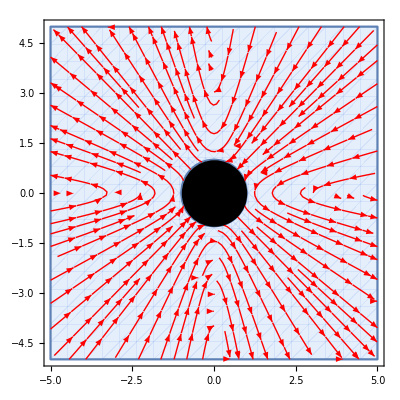

```mathematica
P1= StreamPlot[{{uxp/.{z->0},uyp/.{z->0}}},{x,-xm,xm},{y,-zm,zm},RegionFunction->((a0^2<#1^2+#2^2<xm^2+zm^2)&),StreamColorFunction->(Red&),PlotLegends->{"Full"}];
P2=Graphics[Disk[{0,0},a0]];
Show[P1,P2]
```